Numerov matrix method with  SHO potential

```mathematica
(* Potential, desired max energy *)
V[s_]:=.5 s^2;ϵm=50.;
(* Determine grid *)
rturn=FindRoot[V[s]==ϵm,{s,ϵm}]⟦1,2⟧;d=1/(√(2ϵm));
n=Round[2(rturn/d+4π )];s=Table[-(d (n+1))/2+d i,{i,n}];
(* Calculate KE matrix *)
𝕀[n_,d_]:=DiagonalMatrix[1+0Range[n-Abs[d]],d];
B=1./12(𝕀[n,-1]+10 𝕀[n,0]+𝕀[n,1]);
A=1/d^2(𝕀[n,-1]-2 𝕀[n,0]+𝕀[n,1]);
KE=-1/2 Inverse[B].A;
(* Hamiltonian *)
H=KE+DiagonalMatrix[V[s]];
(* Energies, wavefunctions *)
{eval,evec}=Eigensystem[H];
```

```mathematica
(* Swap list ordering and show first 20 eigenvalues *)
in=Ordering[eval];
```

```mathematica
eval=eval⟦in⟧;evec=evec⟦in⟧;
```

```mathematica
eval⟦;;20⟧
```

{0.5,1.5,2.49999,3.49998,4.49995,5.49991,6.49985,7.49977,8.49967,9.49954,10.4994,11.4992,12.499,13.4987,14.4984,15.498,16.4976,17.4972,18.4966,19.4961}

```mathematica
(* Construct and plot analytical wavefunctions *)
psia[s_,n_]:=π^(-1/4)/(√(2^n*(n)!))Exp[-s^2/2]*HermiteH[n,s];
analytical=Plot[-psia[s,9],{s,-10,10}];
```

```mathematica
Integrate[psia[x,9]^2,{x,-∞,∞}]
```

1

```mathematica
(* Plot Numerov wavefunctions, normalize to 1 *)
f[i_]:=-(d (n+1))/2 +d i
scale=Map[f,Range[Length[evec[[10]]]]];
result=Transpose[{scale,evec[[10]]/√d}];
numerov=ListPlot[result,PlotRange->All];
```

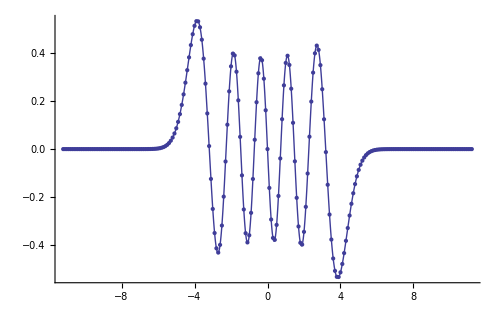

```mathematica
Show[numerov,analytical,ImageSize->500]
```